```mathematica
(* 
*
Program calculating the shape of rod under the load.
Load force is applied to the one end and the other and of rod is clamped.

version 0.0.1

for any questions write to 
Eugene Katrukha: katpyxa@gmail.com
*
*)

(**************************************************)
(* ********       MAIN PARAMETERS        ******** *)
(**************************************************)

(*total length of the rod*)
length= 10.00*10^-6; (*in m*)
(*flexural rigidity*)
EI = 2.2*10^-23; (*in Nm2 *)
(*load*)
force =10.0*10^-12;(*in N*)
(*angle of force application*)
alpha = 60.; (*in degrees*)
(*precision of solution, i.e. number of sampling points along the rod length*)
(*the more the better solution is but takes more time*)
Npoints=51; (* in items *)
(**************************************************)
(* whether or not print debug parameters*)
bDebugPrint = false;

Print["Started.."];
(*converting alpha to radians and model's angle*)
gamma= Pi-alpha*Pi/180;
(*dimensionless parameter*)
beta=Sqrt[force*length*length/EI];
(*let's find essential parameters of the rods' shape*)
params=NMinimize[{Abs[EllipticK[z*z]-EllipticF[phiz,z*z]-beta],z*Sin[phiz]==Sin[0.5*gamma]},{z,phiz}];
(*just getting values*)
k=z/.params[[2]];
phizero=phiz/.params[[2]];
(*symmetry considerations*)
If[phizero<0, phizero=-phizero;k=-k;];
(*curve parametrization*)
phiarray = Table[0,{Npoints}];
xprimearray= Table[0,{Npoints}];
yprimearray= Table[0,{Npoints}];
(*final coordinates of shape*)
xarray= Table[0,{Npoints}];
yarray= Table[0,{Npoints}];
s=0;
ProgressIndicator[Dynamic[s]]
For[i=1,i<Npoints,i++,
tempor = NMinimize[{Abs[s-N[(1/beta)*(EllipticF[m,k*k]-EllipticF[phizero,k*k])]],m≤0.5*Pi,m≥phizero},{m}, Method->{"NelderMead","PostProcess"->False, "RandomSeed"->1796},MaxIterations->200,PrecisionGoal->10,AccuracyGoal->100];
phiarray[[i]]=m/.tempor[[2]];
dzangle=Re[2*ArcSin[k*Sin[phiarray[[i]]]]];

xprimearray[[i+1]]=xprimearray[[i]]+Cos[dzangle]*10^6*length/(Npoints-1);
yprimearray[[i+1]]=yprimearray[[i]]+Sin[dzangle]*10^6*length/(Npoints-1);
If[bDebugPrint,
Print["length=",N[10^6*s*length], "um phi=",phiarray[[i]]," tangent angle=",2*ArcSin[k*Sin[phiarray[[i]]]]*180/Pi];];
s+=1/(Npoints-1);
];
If[bDebugPrint,
Print["length=",N[10^6*s*length], "um phi=",N[Pi/2]," tangent angle=",2*ArcSin[k*Sin[Pi/2]]*180/Pi];];

(*rotation back*)
For[i=1,i<=Npoints,i++,
xarray[[i]]=xprimearray[[i]]*Cos[gamma]+yprimearray[[i]]*Sin[gamma];
yarray[[i]]=yprimearray[[i]]*Cos[gamma]-xprimearray[[i]]*Sin[gamma];
];
Print["Done."];
```

Started..

Done.

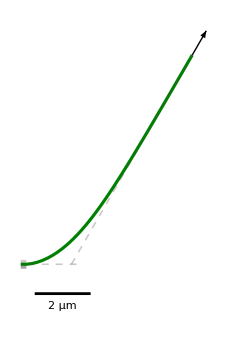

```mathematica
(**************************************************)
(* *********       VIZUALIZATION        ********* *)
(**************************************************)

(* uses output generated by the piece of code above *)
See={Style[Line[Table[{xarray[[i]],yarray[[i]]},{i,1,Npoints/1}]],Thickness[0.01],Darker[Green,.5]],Arrow[{{xarray[[Npoints]],yarray[[Npoints]]},{xarray[[Npoints]]-Cos[gamma],yarray[[Npoints]]+Sin[gamma]}}]};
(*calculate intersection point with x axis*)
slope=-Sin[gamma]/Cos[gamma];
connLength=xarray[[Npoints]]-(yarray[[Npoints]]/slope);
See = Join[See,{Style[Line[{{connLength,0.},{xarray[[Npoints]],yarray[[Npoints]]}}],Dashed,Thickness[0.005], GrayLevel[.3,.3]]}];
See = Join[See,{Style[Line[{{connLength*1.1,0.},{0,0}}],Dashed,Thickness[0.005], GrayLevel[.3,.3]]}];
See = Join[See,{Rectangle[{0.5,-1},{2.5,-1.1}]}];
See = Join[See,{Inset[Style["2 μm", Larger],{1.5,-1.5}]}];
See = Join[See,{Style[Line[{{0.,0.1},{0.2,0.1}}],Thickness[0.01], GrayLevel[.3,.3]]}];
See = Join[See,{Style[Line[{{0.,-0.1},{0.2,-0.1}}],Thickness[0.01], GrayLevel[.3,.3]]}];
See = Join[See,{Style[Line[{{0.,-0.1},{0.2,-0.1}}],Thickness[0.01], GrayLevel[.3,.3]]}];
Graphics[{Arrowheads[Medium],See,ImageSize->{300,300}}]
```

```mathematica
(**************************************************)
(* **********       EXPORT DATA        ********** *)
(**************************************************)

(* Export shape as x and y coordinates *)
filenameExport = "C:\\x_and_y_positions.dat";
Export["",Table[{xarray[[i]],yarray[[i]]},{i,1,Npoints}]]
```